```mathematica
Clear["`*"]
```

```mathematica
position[b_, c_, θ_]:= b  Cos[θ] + c (1 - b^2/c^2 Sin[θ]^2)^(1/2)
```

```mathematica
accel[b_, c_, th_] := Evaluate[D[position[b, c, th], {th, 2}]]
approx[b_,c_,th_]:= -b Cos[th] - b^2/c Cos[2 th]
```

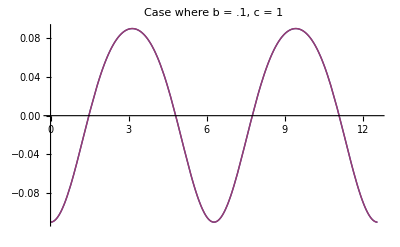

```mathematica
Plot[{accel[.1, 1, x], approx[.1, 1, x]}, {x,0, 4π}, PlotLabel->"Case where b = .1, c = 1"]
```

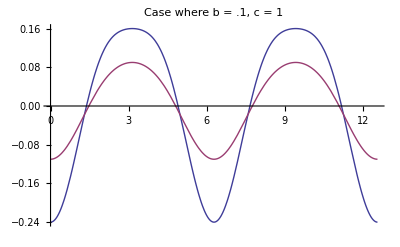

```mathematica
Plot[{accel[.2, 1, x], approx[.1, 1, x]}, {x,0, 4π}, PlotLabel->"Case where b = .2, c = 1"]
```

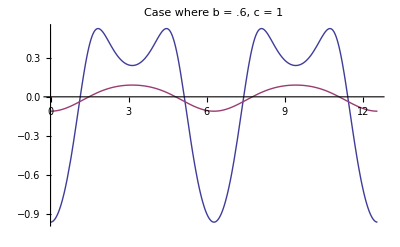

```mathematica
Plot[{accel[.6, 1, x], approx[.1, 1, x]}, {x,0, 4π}, PlotLabel->"Case where b = .6, c = 1"]
```